# Mathematica intro (week 2)

## Differentiation

```mathematica
ClearAll[f];
f[x_]:=Exp[-x^2];
f'[x]                              (*first derivative,prime notation*)
f''[x]                             (*second derivative,prime notation*)
D[f[x],{x,5}]        (*fifth derivative,using the D function*)
```

-2 ⅇ^(-x^2) x

-2 ⅇ^(-x^2)+4 ⅇ^(-x^2) x^2

-120 ⅇ^(-x^2) x+160 ⅇ^(-x^2) x^3-32 ⅇ^(-x^2) x^5

```mathematica
f[x_,y_]:=Exp[-x^2+x*y];
D[f[x,y],x]                             (*derivative with respect to x, fixed y*)
D[f[x,y],{y,2}]                  (*second derivative w.r.t. y, fixed x*)
D[f[x,y],{x,2},{y,1}]  (*second derivative w.r.t. x, first derivative w.r.t. y*)
D[f[x,y],{x,2},{y,1}]  //Simplify
D[f[x,y],{x,2},{y,1}]  //FullSimplify
```

ⅇ^(-x^2+x y) (-2 x+y)

ⅇ^(-x^2+x y) x^2

-2 ⅇ^(-x^2+x y) x+2 ⅇ^(-x^2+x y) (-2 x+y)+ⅇ^(-x^2+x y) x (-2 x+y)^2

ⅇ^(x (-x+y)) (4 x^3+2 y-4 x^2 y+x (-6+y^2))

ⅇ^(x (-x+y)) (2 y+x (-6+(-2 x+y)^2))

## Integration

```mathematica
Integrate[Sec[x],x]
Integrate[Sec[x],{x,0,1}]
```

-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]

2 ArcTanh[Tan[1/2]]

```mathematica
Timing[NIntegrate[Sec[x],{x,0,1}]]
Timing[N[Integrate[Sec[x],{x,0,1}]]]
Timing[Integrate[Sec[x],{x,0,1.}]]
```

{0.02661,1.22619}

{0.47965,1.22619}

{8.86535,1.22619}

## Piecewise functions

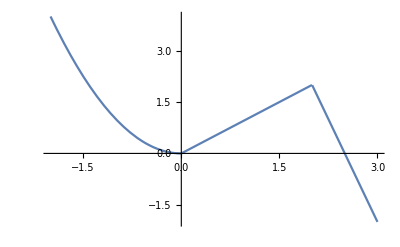

-Graphics-

-Graphics-

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,0<x<2},{10-4x,x≥2}}],{x,-2,3}]
Plot[If[x<0,x^2,If[x<2,x,10-4x]],{x,-2,3}]
Plot[Which[x<0,x^2,0<x<2,x,x≥2,10-4x],{x,-2,3}]
```

## Differential equation solving

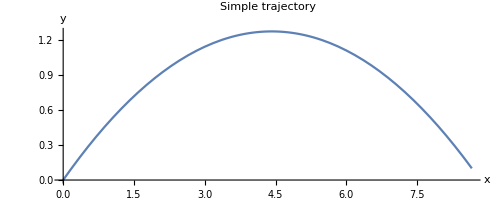

```mathematica
θ=π/6;v0=10;
eqs={y''[t]==-9.8,x''[t]==0};
inits={x'[0]==v0*Cos[θ],y'[0]==v0*Sin[θ], x[0]==0,y[0]==0};
sol=NDSolve[{eqs,inits}, {x,y},{t,0,10}][[1]];
ParametricPlot[{x[t],y[t]}/.sol, {t,0,1},PlotLabel->"Simple trajectory",AxesLabel->{"x","y"}]
```

{y→Function[{t},5. t-4.9 t^2],x→Function[{t},5 √3 t]}

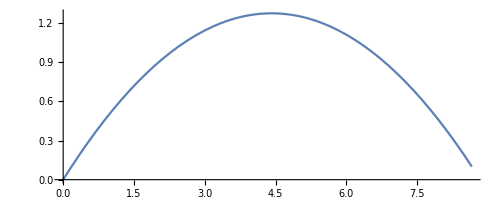

```mathematica
θ=π/6;v0=10;
sol=DSolve[{eqs, inits}, {y,x},t][[1]]
ParametricPlot[{x[t],y[t]}/.sol,{t,0,1}]
```

## Finding Roots

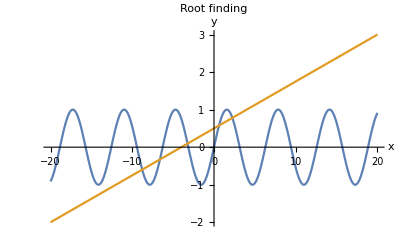

```mathematica
y1[x_]:=Sin[x];
y2[x_]:=(4+x)/8;
Plot[{y1[x],y2[x]},{x,-20,20},PlotLabel->"Root finding",AxesLabel->{"x","y"}]
```

```mathematica
FindRoot[y1[x]-y2[x],{x,-9}]
FindRoot[y1[x]-y2[x],{x,-7}]
FindRoot[y1[x]-y2[x],{x,-3}]
FindRoot[y1[x]-y2[x],{x,1}]
FindRoot[y1[x]-y2[x],{x,2}]
FindRoot[y1[x]-y2[x],{x,{-9,-7,-2,2}}]
```

{x→-8.7838}

{x→-6.61636}

{x→-3.2371}

{x→0.614879}

{x→2.24577}

{x→{-8.7838,-6.61636,-3.2371,2.24577}}

## Solving systems of equations

```mathematica
Clear[x,y,z] (*make sure values not set, check variable colours*)
Solve[{2x+3y-z==-13, x-6y+4z==7,-6x-2y+2z==52},{x,y,z}]
```

{{x→-7,y→3,z→8}}

-Graphics-

## The bakery problem

```mathematica
(*c = packs of croissant, m = packs of muffins, b = packs of bagels *)
Clear[c,b,m];(*c used earlier, good to clear all.*)
Solve[{
30 c + 18 b + 12 m == 642,
76.60 c +45.20 b + 23.10 m ==1523.10,
c≥0, b ≥ 0, m≥ 0}, {c,b,m},Integers]
(*Error resulting from the fact that the numbers are real. Multiply through equations by 100 (10 would suffice) to make numnbers integers, then error goes away.*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c→13,b→4,m→15}}

```mathematica
Solve[{
30 c + 18 b + 12 m == 642,
7660 c +4520 b + 2310 m ==152310,
c≥0, b ≥ 0, m≥ 0}, {c,b,m},Integers]
```

{{c→13,b→4,m→15}}

## Using strings

```mathematica
str=" this string ";
(*there is a space at the start and end, won't get {{6,9}} as answer later if these are missed*)
a=45;
StringLength[str]
str1="abcd"<>str<>"xyz"<>ToString[a]
StringLength[str1]
```

13

abcd this string xyz45

22

```mathematica
StringTake[str1,{6,17}]
StringPosition[str1,"this"]
StringReplace[str1,"this"->"that"]
```

this string

{{6,9}}

abcd that string xyz45

```mathematica
Characters["abcd that string xyz45"]
```

{a,b,c,d, ,t,h,a,t, ,s,t,r,i,n,g, ,x,y,z,4,5}

From the StringPosition help file entry: 
“StringPosition[“string”,”sub”] gives a list of the starting and ending character positions at which “sub” appears as a substring of “string”.”
So “this” starts at character 6 and finishes at character 9 in str1.

## Cell formatting

```mathematica
path="https://www.st-andrews.ac.uk/~ph3080/";
NotebookOpen[path<>"intro/SampleNotebook.nb"]
```

qjiyp_shm18FrontEndObject[LinkObject["qjiyp_shm", 3, 1]]18Sample Notebook/var/folders/vx/3rsx919s1fdbyk_tm731m7jc0000gn/T/www.st-andrews.ac.uk/~ph3080/intro/SampleNotebook.nb

## Using data files

### Sudoku

```mathematica
data=Import[path<>"intro/sudoku.csv","CSV"]
```

{{4,3,5,2,6,9,7,8,1},{6,8,2,5,7,1,4,9,3},{1,9,7,8,3,4,5,6,2},{8,2,6,1,9,5,3,4,7},{3,7,4,6,8,4,9,1,5},{9,5,1,7,4,3,6,2,8},{5,1,9,3,2,6,8,7,4},{2,4,8,9,5,7,1,3,6},{7,6,3,4,1,8,2,5,9}}

```mathematica
Grid[data,Dividers->All]
Total[data]
Total[Transpose[data]]
```

4 | 3 | 5 | 2 | 6 | 9 | 7 | 8 | 1
6 | 8 | 2 | 5 | 7 | 1 | 4 | 9 | 3
1 | 9 | 7 | 8 | 3 | 4 | 5 | 6 | 2
8 | 2 | 6 | 1 | 9 | 5 | 3 | 4 | 7
3 | 7 | 4 | 6 | 8 | 4 | 9 | 1 | 5
9 | 5 | 1 | 7 | 4 | 3 | 6 | 2 | 8
5 | 1 | 9 | 3 | 2 | 6 | 8 | 7 | 4
2 | 4 | 8 | 9 | 5 | 7 | 1 | 3 | 6
7 | 6 | 3 | 4 | 1 | 8 | 2 | 5 | 9

{45,45,45,45,45,47,45,45,45}

{45,45,45,45,47,45,45,45,45}

-Graphics-

```mathematica
(*spot the out-of-place 47's *)
data[[5,6]]=2;
Grid[data,Dividers->All]
Total[data]
Total[Transpose[data]]
```

4 | 3 | 5 | 2 | 6 | 9 | 7 | 8 | 1
6 | 8 | 2 | 5 | 7 | 1 | 4 | 9 | 3
1 | 9 | 7 | 8 | 3 | 4 | 5 | 6 | 2
8 | 2 | 6 | 1 | 9 | 5 | 3 | 4 | 7
3 | 7 | 4 | 6 | 8 | 2 | 9 | 1 | 5
9 | 5 | 1 | 7 | 4 | 3 | 6 | 2 | 8
5 | 1 | 9 | 3 | 2 | 6 | 8 | 7 | 4
2 | 4 | 8 | 9 | 5 | 7 | 1 | 3 | 6
7 | 6 | 3 | 4 | 1 | 8 | 2 | 5 | 9

{45,45,45,45,45,45,45,45,45}

{45,45,45,45,45,45,45,45,45}

```mathematica
(*You can divide the grid up using the Dividers option, making it look like a "proper" sudoku grid. *)
Grid[data,Dividers->{{{True,False,False}},{{True,False,False}}}]
```

4 | 3 | 5 | 2 | 6 | 9 | 7 | 8 | 1
6 | 8 | 2 | 5 | 7 | 1 | 4 | 9 | 3
1 | 9 | 7 | 8 | 3 | 4 | 5 | 6 | 2
8 | 2 | 6 | 1 | 9 | 5 | 3 | 4 | 7
3 | 7 | 4 | 6 | 8 | 2 | 9 | 1 | 5
9 | 5 | 1 | 7 | 4 | 3 | 6 | 2 | 8
5 | 1 | 9 | 3 | 2 | 6 | 8 | 7 | 4
2 | 4 | 8 | 9 | 5 | 7 | 1 | 3 | 6
7 | 6 | 3 | 4 | 1 | 8 | 2 | 5 | 9

### Data import and fitting

-Graphics-

```mathematica
imp=Import[path<>"/intro/datafile.txt","Data"];
```

{a0→87.3517,a1→5.02137,a2→1235.94}

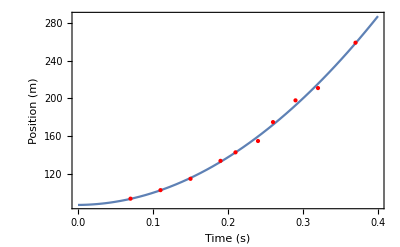

```mathematica
data=imp[[3;;-1]]; (* could use [[3;;]] to end *)
model=a0+a1 x+a2 x^2;
fit=FindFit[data,model,{a0,a1,a2},x]
Plot[model/.fit,{x,0,0.4},Epilog->{Red,Point[data]}, Frame->True, FrameLabel->{"Time (s)","Position (m)"}]
```

### Working with image data (star field)

{363,480}

21124.5

241.573

181.946

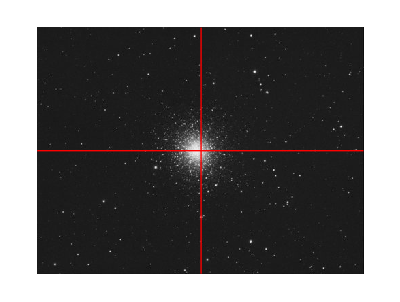

```mathematica
(*if they cut/paste this then look out for xMean and yMean containing symbols ximgData & yimgData instead a product.*)
filename=path<>"intro/CoG_image.jpg";
img=Import[filename];
imgData=N[ImageData[img]];(*N[] turns data to floating point numbers for speed*){yMax,xMax}=Dimensions[imgData]
totI=Total[imgData,2]
xMean=Sum[x imgData[[y,x]],{y,1,yMax},{x,1,xMax}]/totI
yMean=Sum[y imgData[[y,x]],{y,1,yMax},{x,1,xMax}]/totI
Graphics[{Raster[imgData],{Red,Line[{{1,yMean},{xMax,yMean}}],Line[{{xMean,1},{xMean,yMax}}]}}]
```

### Working with image data (circle plot)

```mathematica
filename=path<>"intro/circle.jpg";
img=Import[filename];
imgData=N[ImageData[img]];(*N[] turns data to floating point numbers for speed*){yMax,xMax}=Dimensions[imgData]
totI=Total[imgData,2]
xMean=Sum[x imgData[[y,x]],{y,1,yMax},{x,1,xMax}]/totI
yMean=Sum[y imgData[[y,x]],{y,1,yMax},{x,1,xMax}]/totI
Graphics[{Raster[imgData],{Red,Line[{{1,yMean},{xMax,yMean}}],Line[{{xMean,1},{xMean,yMax}}]}}]
```

{500,500}

179.847

329.251

126.595

-Graphics-

## Oil pipeline cost problem

-Graphics-

```mathematica
onLandCost[x_]:=0.3Sqrt[x^2+20^2]
```

-Graphics-

```mathematica
atSeaCost[x_]:=1 Sqrt[(100-x)^2+60^2]
```

-Graphics-

```mathematica
sol=NMinimize[onLandCost[x]+atSeaCost[x],x]
```

{87.9624,{x→81.7226}}

This is the minimum cost (first part of list, and the value of x at which it occurs.

-Graphics-

```mathematica
θ1=ArcTan[x/20]/.sol[[2]] (*in radians*)
θ1/Degree (*show in degrees*)
```

1.33078

76.2483

```mathematica
θ2=ArcTan[(100-x)/60]/.sol[[2]] (*in radians*)
θ2/Degree (*show in degrees*)
```

0.295693

16.942

-Graphics-

```mathematica
Sin[θ1]/Sin[θ2]
1/0.3
```

3.3333

3.33333

Snell’s Law!!

## Pure functions

```mathematica
ClearAll[f];
f[x_]:=10 x
f[3]
Function[x,10x][3]
10#&[3]
```

30

30

30

```mathematica
(*threshold function - values capped at 10*)
Map[If[#>10,10,#]&,{5,3,1,11,7,15,2}]
```

{5,3,1,10,7,10,2}

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},PlotLabel->"Plot of Sin[x y]",  AxesLabel->{"x","y"},ColorFunction->(GrayLevel[#]&)]
Plot3D[Sin[x y],{x,0,3},{y,0,3},PlotLabel->"Plot of Sin[x y]",  AxesLabel->{"x","y"},ColorFunction->(GrayLevel[#1]&)]
Plot3D[Sin[x y],{x,0,3},{y,0,3},PlotLabel->"Plot of Sin[x y]",  AxesLabel->{"x","y"},ColorFunction->(GrayLevel[#2]&)]
Plot3D[Sin[x y],{x,0,3},{y,0,3},PlotLabel->"Plot of Sin[x y]",  AxesLabel->{"x","y"},ColorFunction->(GrayLevel[#3]&)]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

The details section in the ColorFunction’s help file entry shows us that three arguments are passed to the ColorFunction from Plot3D. These are x, y and z, and are respectively in slots 1, 2, and 3. You can see the GreyLevel varying with x if #1 is used, y with #2 and z with #3. # alone is equivalent to #1. 
Strangely, there seems to be a fourth argument passed in slot #4, but what this is I do not know. Suggestions on a postcard.

## Programming with rules and patterns

```mathematica
2x+y/.{x->5,y->3}
```

13

```mathematica
{1,−23,−3.5,4.1,7}/.x_Integer->0
{1,−23,−3.5,4.1,7}/.x_?Negative->0
```

{0,0,-3.5,4.1,0}

{1,0,0,4.1,7}

```mathematica
Head[5] 
Head[Negative]
```

Integer

Symbol

```mathematica
Clear[p,q]
{{1,2},{3,4},{5,6}}/.{p_,q_}->{q,p}
```

{{2,1},{4,3},{6,5}}

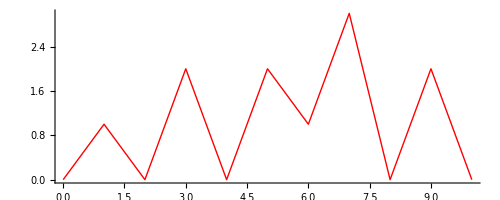

```mathematica
g=Graphics[{Red,Line[{{0.0,0.0},{1.0,1.0},{2.0,0.0},{3.0,2.0},{4.0,0.0},{5.0,2.0},{6.0,1.0},{7.0,3.0},{8.0,0.0},{9.0,2.0},{10.0,0.0}}]},Axes->True]
```

-Graphics-

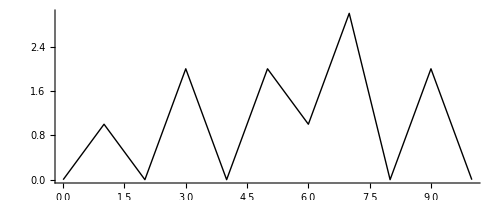

```mathematica
g/.{p_,q_}->{q,p} 
(*this switches Red and Line as it is two things in a list, then does not recurse down the list levels*)
```

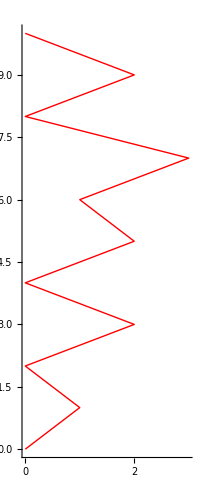

```mathematica
g/.{p_?NumericQ,q_?NumericQ}->{q,p}
(*this specifies that it should only look for two numbers in a list, and switch them*)
```

```mathematica
g/.{p_Real,q_Real}->{q,p}
(*this is a possible solution, but be careful that Integer is not a subset of Real, try making one of the points have an integer x or y coordinate*)
```

-Graphics-

#### Typed from student sheet

```mathematica
(*define first fractal using a replacement rule*)
frac1={p->3.,c->c1+I c2};
(*build fractal list by rastering over c1& c2*)
ifrac1=Table[z=0.0;
(*iteratively calculate z for 10 steps*)
Do[z=z^p+c/.frac1,{i,10}];
(*output 1 when final z is over threshold and zero otherwise*)
If[Abs[z]>1,1,0],{c1,1,-2,-0.01},{c2,-1.5,1.5,0.01}];
(*Display output*)
ListDensityPlot[ifrac1,PlotRange->All,DataRange->{{-1.5,1.5},{-2,1}},FrameLabel->{"c2","c1"}]
```

-Graphics-

-Graphics-

```mathematica
frac2=frac1/.{(p->a_)->(p->2)};  (*change power value*)
```

-Graphics-

```mathematica
ifrac2=Table[z=0.0;
(*iteratively calculate z for 10 steps*)
Do[z=z^p+c/.frac2,{i,10}];
(*output 1 when final z is over threshold and zero otherwise*)
If[Abs[z]>1,1,0],{c1,1,-2,-0.01},{c2,-1.5,1.5,0.01}];
(*Display output*)
ListDensityPlot[ifrac2,PlotRange->All,DataRange->{{-1.5,1.5},{-2,1}},FrameLabel->{"c2","c1"}]
```

-Graphics-

-Graphics-

```mathematica
z=0;
ta=Do[z=z^p+c/.frac2/.{c1->0.4,c2->0.4},{i,10}]
z
```

0.808082-3.62088 ⅈ

-Graphics-

```mathematica
z=0;
ta=Table[z=z^p+c/.frac2/.{c1->0.4,c2->0.4},{i,10}];
Select[ta,Re[#]<0&]
```

{-0.550845+0.481203 ⅈ,-1.49158+1.34786 ⅈ}

## Patterns in functions

```mathematica
prob[n_Integer]:=(6-Abs[n-7])/36;
```

-Graphics-

```mathematica
prob[10]
prob[2]
```

1/12

1/36

-Graphics-

```mathematica
prob[3.7]
(* the function is not defined for a real-valued argument, so just echoes back the input *)
```

prob[3.7]

-Graphics-

```mathematica
probs=Table[prob[n],{n,2,12}]
Total[probs]
```

{1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36}

1

-Graphics-

```mathematica
ClearAll[prob];
prob[n_Integer/;2≤n≤12]:=(6-Abs[n-7])/36;
probs=Table[prob[n],{n,1,15}]
```

{prob[1],1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36,prob[13],prob[14],prob[15]}

```mathematica
ClearAll[f];Clear[a];(*Always good practice to clear key symbols*)
f[a_]:=NIntegrate[a x^2,{x,-1,1}]
f[2]
f[a]
```

1.33333

NIntegrate::inumr: The integrand a x^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate[a x^2,{x,-1,1}]

```mathematica
ClearAll[f];Clear[a];
f[a_?NumericQ]:=NIntegrate[a x^2,{x,-1,1}]
f[2]
f[a]
```

1.33333

f[a]

## Solving differential equations with triggering events

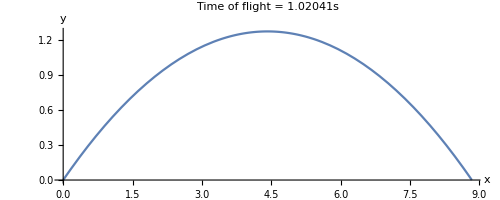

```mathematica
θ=π/6;v0=10;
eqs={y''[t]==-9.8,x''[t]==0};
inits={x'[0]==v0*Cos[θ],y'[0]==v0*Sin[θ],x[0]==0,y[0]==0};
event=WhenEvent[y[t]==0,timeofflight=t];
sol=NDSolve[{eqs,inits,event},{x,y},{t,0,10}][[1]];
ParametricPlot[{x[t],y[t]}/.sol,{t,0,timeofflight},PlotLabel->"Time of flight = "<>ToString[timeofflight]<>"s",AxesLabel->{"x","y"}]
```

-Graphics-

```mathematica
θ=π/6;v0=10;
eqs={y''[t]==-9.8,x''[t]==0};
inits={x'[0]==v0*Cos[θ],y'[0]==v0*Sin[θ],x[0]==0,y[0]==0};
event=WhenEvent[y[t]==0,timeofflight=t;"StopIntegration"];
sol=NDSolve[{eqs,inits,event},{x,y},{t,0,10}][[1]]
ParametricPlot[{x[t],y[t]}/.sol,{t,0,timeofflight},PlotLabel->"Time of flight = "<>ToString[timeofflight]<>"s",AxesLabel->{"x","y"}]
(* with the semi-solon removed from the end of teh sol statement, we can see that the (time) Domain in the InterpolatingFunction is from {0,1.02}. This tells us that integration has stopped when our WhenEvent was triggered. *)
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

-Graphics-

## Solving differential equations for parametric study

```mathematica
v0=10;
tof[θ_]:=Module[{eqs,inits,event,timeofflight,sol},
eqs={y''[t]==-9.8,x''[t]==0};
inits={x'[0]==v0*Cos[θ],y'[0]==v0*Sin[θ],x[0]==0,y[0]==0};
event=WhenEvent[y[t]==0,timeofflight=t;"StopIntegration"];
sol=NDSolve[{eqs,inits,event},{x,y},{t,0,10}][[1]];
timeofflight]
```

```mathematica
tof[π/4]
```

1.44308

-Graphics-

```mathematica
dof[θ_]:=Module[{eqs,inits,event,timeofflight,sol},
eqs={y''[t]==-9.8,x''[t]==0};
inits={x'[0]==v0*Cos[θ],y'[0]==v0*Sin[θ],x[0]==0,y[0]==0};
event=WhenEvent[y[t]==0,timeofflight=t;"StopIntegration"];
sol=NDSolve[{eqs,inits,event},{x,y},{t,0,10}][[1]];
x[timeofflight]/.sol]
```

-Graphics-

```mathematica
toflist=Table[Flatten[{θ,tof[θ], dof[θ]}],{θ,0.02,π/2,0.02}]
```

{{0.02,0.0408136,0.408054},{0.04,0.0816109,0.815456},{0.06,0.122376,1.22155},{0.08,0.163091,1.6257},{0.1,0.203742,2.02724},{0.12,0.244311,2.42554},{0.14,0.284782,2.81996},{0.16,0.325139,3.20986},{0.18,0.365366,3.59464},{0.2,0.405448,3.97366},{0.22,0.445367,4.34632},{0.24,0.485107,4.71203},{0.26,0.524654,5.07021},{0.28,0.563991,5.42027},{0.3,0.603102,5.76166},{0.32,0.641973,6.09383},{0.34,0.680586,6.41626},{0.36,0.718927,6.72842},{0.38,0.756981,7.02981},{0.4,0.794731,7.31996},{0.42,0.832164,7.5984},{0.44,0.869264,7.86468},{0.46,0.906017,8.11838},{0.48,0.942406,8.3591},{0.5,0.978419,8.58644},{0.52,1.01404,8.80004},{0.54,1.04926,8.99957},{0.56,1.08405,9.1847},{0.58,1.11842,9.35513},{0.6,1.15233,9.5106},{0.62,1.18579,9.65086},{0.64,1.21877,9.77567},{0.66,1.25126,9.88485},{0.68,1.28325,9.97821},{0.7,1.31473,10.0556},{0.72,1.34568,10.1169},{0.74,1.3761,10.162},{0.76,1.40596,10.1909},{0.78,1.43526,10.2035},{0.8,1.46399,10.1997},{0.82,1.49213,10.1797},{0.84,1.51968,10.1433},{0.86,1.54662,10.0907},{0.88,1.57294,10.022},{0.9,1.59863,9.93722},{0.92,1.62368,9.83656},{0.94,1.64808,9.72017},{0.96,1.67182,9.58822},{0.98,1.69489,9.44093},{1.,1.71729,9.27855},{1.02,1.739,9.10131},{1.04,1.76001,8.90952},{1.06,1.78032,8.70347},{1.08,1.79991,8.4835},{1.1,1.81879,8.24996},{1.12,1.83694,8.00322},{1.14,1.85435,7.74368},{1.16,1.87103,7.47175},{1.18,1.88695,7.18786},{1.2,1.90212,6.89248},{1.22,1.91653,6.58607},{1.24,1.93017,6.26913},{1.26,1.94304,5.94215},{1.28,1.95513,5.60567},{1.3,1.96645,5.26022},{1.32,1.97697,4.90635},{1.34,1.9867,4.54464},{1.36,1.99564,4.17565},{1.38,2.00378,3.79999},{1.4,2.01112,3.41825},{1.42,2.01766,3.03103},{1.44,2.02338,2.63897},{1.46,2.0283,2.24269},{1.48,2.03241,1.84282},{1.5,2.0357,1.44},{1.52,2.03818,1.03488},{1.54,2.03985,0.628099},{1.56,2.0407,0.220316}}

-Graphics-

```mathematica
Dimensions[toflist]
```

{78,3}

-Graphics-

```mathematica
max=Max[toflist[[All,3]]]
```

10.2035

-Graphics-

```mathematica
pos=Position[toflist,max][[1,1]]
(*returns a list of positions, we only want one, and take first value from that position.*)
```

39

-Graphics-

```mathematica
maxtheta=toflist[[pos]][[1]]
π/4.
```

0.78

0.785398

-Graphics-

```mathematica
(*use a finer grained list of theta values in our look-up table.*)
toflist2=Table[{θ,tof[θ],dof[θ]},{θ,0.77,0.79,0.0001}];
Dimensions[toflist2]
max=Max[toflist2[[All,3]]]
pos2=Position[toflist2,max][[1,1]]
maxtheta2=toflist2[[pos2]][[1]]
```

{201,3}

10.2041

155

0.7854

-Graphics-

```mathematica
(*Note that θ has been set earlier and so needs cleared. 
There are two "expected" warning messages as FindMaximum tried to evaluate tof[θ] algebraically twice for the Automatic method (method switching here?),
there is no definition for symbolic tof[θ]and the second part therefore does not exist.*)

ClearAll[dof]
Clear[θ]
v0=10;
dof[θ_?NumericQ]:=Module[{eqs,inits,event,timeofflight,sol},
eqs={y''[t]==-9.8,x''[t]==0};
inits={x'[0]==v0*Cos[θ],y'[0]==v0*Sin[θ],x[0]==0,y[0]==0};
event=WhenEvent[y[t]==0,timeofflight=t;"StopIntegration"];
sol=NDSolve[{eqs,inits,event},{x,y},{t,0,10}][[1]];
x[timeofflight]/.sol]
FindMaximum[dof[θ],θ,AccuracyGoal->6]
```

{10.2041,{θ→0.785398}}

## Debugging methods

-Graphics-

```mathematica
NotebookOpen[path<>"intro/abird.nb"]
```

qjiyp_shm19FrontEndObject[LinkObject["qjiyp_shm", 3, 1]]19abird.nb/var/folders/vx/3rsx919s1fdbyk_tm731m7jc0000gn/T/www.st-andrews.ac.uk/~ph3080/intro/abird.nb

### Corrected angry-birds code

```mathematica
g={0,-9.81};
γ=0.03;m=.2(*values of g, γ and m corrected *);
sol3[α_,v0_,w_]:=Module[{t,sol,hit},
sol=NDSolve[{
m r''[t]==m g - γ (r'[t]-{w,0}),  (* m added here *)
r'[0]==v0{Cos[α],Sin[α]},
r[0]=={0,0},
WhenEvent[r[t][[2]]==0 ,hit=t; "StopIntegration"]},r,{t,0,100}];
{sol,hit}];

Manipulate[
sol=sol3[α Degree,v0,wind][[1]]; (* watch 0 and O *)
tof=sol3[α Degree,v0,wind][[2]];
pp=ParametricPlot[r[t]/.sol,{t,0,tof},Epilog->{Orange,PointSize[Large], (* watch spelling *)
Point[{38,0.5}],Darker[Green],Thick,Arrow[{{20,10},{20+wind,10}}],Text["Wind",{20,12}]},PlotRange->{{0,40},{0,14}}],{{α,30},10 ,60},{{v0,12},10,20},{{wind,5},-20,20}]
```